```mathematica
Clear["Global`*"]
```

### Model

```mathematica
a= 1.42; a0=2 √3 a;
a1=a0{1/2 √3,-1/2};  a2=a0{1/2 √3,1/2};
δ1=a{-1/2,(√3)/2};δ2=a{-1/2,(-√3)/2};δ3=a{1,0};

(* == CsGraphene Parameters  == *)
t0=-2.7 ; 
μVHSs={0.431523,0.839523,0.889523,1.413857,1.733857};
Hk=With[{δ1=a{-1/2,(√3)/2},δ2=a{-1/2,(-√3)/2},δ3=a{1,0},
(*old params*)
(*
ϵc =0.5 t0,
ϵcp =0.52 t0 ,
ϵcs =-0.4 t0 , 
t = 1.1 t0,
tp =1.1 t0 ,
t2 = 0.015 t0,
t3 = 0.1 t0 ,
th =0.025 t0,
tcs = 0.12t0,
tcs2 = 0 t0 
*)
(*mod by hand:*)
(*
ϵc =0.97t0,
ϵcp =0.98t0 ,
ϵcs =-0.09t0, 
t = -3.35,
tp =-3.35,
t2 = -0.5,
t3 = -0.41,
th =0.07 t0 ,
tcs = 0.095t0 ,
tcs2 =-0.02t0 ,
tcs3 =0
*)
(*new params guille*)
ϵc =0.259t0,
ϵcp =0.304 t0,
ϵcs =-0.385 t0 ,
t = t0,
tp = t0,
t2 =-0.083 t0,
t3 = 0.056 t0 ,
tcs = 0.172t0 ,
tcs2 = -0.059 t0 ,
th = 0.012 t0 4 ,
tcs3 =0.00 t0

},
Compile[{{k,_Real,1}},
Module[{kx,ky,f1,f2,f3,c12,c23,c31,h1,h2,h3,hcs,sol},
{kx,ky}=k;
f1=Exp[ⅈ δ1.k];
f2=Exp[ⅈ δ2.k];
f3=Exp[ⅈ δ3.k];
c12=2Cos[(δ1-δ2).k];
c23=2Cos[(δ2-δ3).k];
c31=2Cos[(δ3-δ1).k];
h3=t3 (Exp[ⅈ k.(δ1-δ2-δ3)]+Exp[ⅈ k.(-δ1+δ2-δ3)]+Exp[ⅈ k.(-δ1-δ2+δ3)]);
hcs=ϵcs+2tcs(Cos[2 (δ1-δ3).k]+Cos[2(δ2-δ3).k]+Cos[2(δ1-δ2).k]) +2tcs2(Cos[6 δ1.k]+Cos[6δ2.k]+Cos[6δ3.k])+2tcs3(Cos[4 (δ1-δ3).k]+Cos[4(δ2-δ3).k]+Cos[4(δ1-δ2).k]);
sol=
{
{ϵc,t f3,t2 c23,t2 c31,t f2,t f1, t2 c12,h3*,0},
{t f3*,ϵcp,tp f2*,tp f1*,t2 c23, t2 c31, h3, t2 c12, th f3},
{t2 c23,tp f2, ϵcp, t2 c12, tp f3, h3*, t2 c31, t f1, th f1*},
{t2 c31, tp f1, t2 c12, ϵcp, h3*, tp f3, t2 c23, t f2, th f2*},
{t f2*,t2 c23, tp f3*,h3,ϵcp,t2 c12, tp f1*, t2 c31, th f2},
{t f1*, t2 c31, h3,tp f3*, t2 c12, ϵcp, tp f2*, t2 c23, th f1},
{t2 c12,h3*,t2 c31, t2 c23, tp f1, tp f2, ϵcp,t f3,th f3*},
{h3, t2 c12, t f1*,t f2*, t2 c31, t2 c23, t f3*, ϵc,0},
{0, th f3*, th f1,th f2, th f2*, th f1*,th f3, 0, hcs}
};
sol],RuntimeAttributes->{Listable}, CompilationTarget->"C",RuntimeOptions->"Speed"]];
(*Numerical derivative (with respect to kx) of Hk as defined above:*)
vx=With[{},
Compile[{{k,_Real,1}},
Module[{kx,ky,sol},
{kx,ky}=k;
sol={{0,(0.-3.834 ⅈ) ⅇ^(ⅈ (0.+1.42 kx)),-0.954666 Sin[2.13 kx+1.2297560733739028 ky],-0.954666 Sin[2.13 kx-1.2297560733739028 ky],(0.+1.917 ⅈ) ⅇ^(ⅈ (-0.71 kx-1.2297560733739028 ky)),(0.+1.917 ⅈ) ⅇ^(ⅈ (-0.71 kx+1.2297560733739028 ky)),0,-0.1512 (((0.-1.42 ⅈ) ⅇ^(ⅈ (-1.42 kx-2.4595121467478056 ky))-(0.+1.42 ⅈ) ⅇ^(ⅈ (-1.42 kx+2.4595121467478056 ky))) Conjugate[ⅇ^(ⅈ (-1.42 kx-2.4595121467478056 ky))+ⅇ^(ⅈ (-1.42 kx+2.4595121467478056 ky))]-(0.+2.84 ⅈ) ⅇ^(-ⅈ (0.+2.84 Conjugate[kx])) Conjugate[kx]),0},{(0.+3.834 ⅈ) ⅇ^(-ⅈ (0.+1.42 Conjugate[kx])) Conjugate[kx],0,(0.-1.917 ⅈ) ⅇ^(-ⅈ (-0.71 Conjugate[kx]-1.2297560733739028 Conjugate[ky])) Conjugate[kx],(0.-1.917 ⅈ) ⅇ^(-ⅈ (-0.71 Conjugate[kx]+1.2297560733739028 Conjugate[ky])) Conjugate[kx],-0.954666 Sin[2.13 kx+1.2297560733739028 ky],-0.954666 Sin[2.13 kx-1.2297560733739028 ky],-0.1512 ((0.+2.84 ⅈ) ⅇ^(ⅈ (0.+2.84 kx))-(0.+1.42 ⅈ) ⅇ^(ⅈ (-1.42 kx-2.4595121467478056 ky))-(0.+1.42 ⅈ) ⅇ^(ⅈ (-1.42 kx+2.4595121467478056 ky))),0,(0.-0.18403200000000003 ⅈ) ⅇ^(ⅈ (0.+1.42 kx))},{-0.954666 Sin[2.13 kx+1.2297560733739028 ky],(0.+1.917 ⅈ) ⅇ^(ⅈ (-0.71 kx-1.2297560733739028 ky)),0,0,(0.-3.834 ⅈ) ⅇ^(ⅈ (0.+1.42 kx)),-0.1512 (((0.-1.42 ⅈ) ⅇ^(ⅈ (-1.42 kx-2.4595121467478056 ky))-(0.+1.42 ⅈ) ⅇ^(ⅈ (-1.42 kx+2.4595121467478056 ky))) Conjugate[ⅇ^(ⅈ (-1.42 kx-2.4595121467478056 ky))+ⅇ^(ⅈ (-1.42 kx+2.4595121467478056 ky))]-(0.+2.84 ⅈ) ⅇ^(-ⅈ (0.+2.84 Conjugate[kx])) Conjugate[kx]),-0.954666 Sin[2.13 kx-1.2297560733739028 ky],(0.+1.917 ⅈ) ⅇ^(ⅈ (-0.71 kx+1.2297560733739028 ky)),(0.-0.09201600000000001 ⅈ) ⅇ^(-ⅈ (-0.71 Conjugate[kx]+1.2297560733739028 Conjugate[ky])) Conjugate[kx]},{-0.954666 Sin[2.13 kx-1.2297560733739028 ky],(0.+1.917 ⅈ) ⅇ^(ⅈ (-0.71 kx+1.2297560733739028 ky)),0,0,-0.1512 (((0.-1.42 ⅈ) ⅇ^(ⅈ (-1.42 kx-2.4595121467478056 ky))-(0.+1.42 ⅈ) ⅇ^(ⅈ (-1.42 kx+2.4595121467478056 ky))) Conjugate[ⅇ^(ⅈ (-1.42 kx-2.4595121467478056 ky))+ⅇ^(ⅈ (-1.42 kx+2.4595121467478056 ky))]-(0.+2.84 ⅈ) ⅇ^(-ⅈ (0.+2.84 Conjugate[kx])) Conjugate[kx]),(0.-3.834 ⅈ) ⅇ^(ⅈ (0.+1.42 kx)),-0.954666 Sin[2.13 kx+1.2297560733739028 ky],(0.+1.917 ⅈ) ⅇ^(ⅈ (-0.71 kx-1.2297560733739028 ky)),(0.-0.09201600000000001 ⅈ) ⅇ^(-ⅈ (-0.71 Conjugate[kx]-1.2297560733739028 Conjugate[ky])) Conjugate[kx]},{(0.-1.917 ⅈ) ⅇ^(-ⅈ (-0.71 Conjugate[kx]-1.2297560733739028 Conjugate[ky])) Conjugate[kx],-0.954666 Sin[2.13 kx+1.2297560733739028 ky],(0.+3.834 ⅈ) ⅇ^(-ⅈ (0.+1.42 Conjugate[kx])) Conjugate[kx],-0.1512 ((0.+2.84 ⅈ) ⅇ^(ⅈ (0.+2.84 kx))-(0.+1.42 ⅈ) ⅇ^(ⅈ (-1.42 kx-2.4595121467478056 ky))-(0.+1.42 ⅈ) ⅇ^(ⅈ (-1.42 kx+2.4595121467478056 ky))),0,0,(0.-1.917 ⅈ) ⅇ^(-ⅈ (-0.71 Conjugate[kx]+1.2297560733739028 Conjugate[ky])) Conjugate[kx],-0.954666 Sin[2.13 kx-1.2297560733739028 ky],(0.+0.09201600000000001 ⅈ) ⅇ^(ⅈ (-0.71 kx-1.2297560733739028 ky))},{(0.-1.917 ⅈ) ⅇ^(-ⅈ (-0.71 Conjugate[kx]+1.2297560733739028 Conjugate[ky])) Conjugate[kx],-0.954666 Sin[2.13 kx-1.2297560733739028 ky],-0.1512 ((0.+2.84 ⅈ) ⅇ^(ⅈ (0.+2.84 kx))-(0.+1.42 ⅈ) ⅇ^(ⅈ (-1.42 kx-2.4595121467478056 ky))-(0.+1.42 ⅈ) ⅇ^(ⅈ (-1.42 kx+2.4595121467478056 ky))),(0.+3.834 ⅈ) ⅇ^(-ⅈ (0.+1.42 Conjugate[kx])) Conjugate[kx],0,0,(0.-1.917 ⅈ) ⅇ^(-ⅈ (-0.71 Conjugate[kx]-1.2297560733739028 Conjugate[ky])) Conjugate[kx],-0.954666 Sin[2.13 kx+1.2297560733739028 ky],(0.+0.09201600000000001 ⅈ) ⅇ^(ⅈ (-0.71 kx+1.2297560733739028 ky))},{0,-0.1512 (((0.-1.42 ⅈ) ⅇ^(ⅈ (-1.42 kx-2.4595121467478056 ky))-(0.+1.42 ⅈ) ⅇ^(ⅈ (-1.42 kx+2.4595121467478056 ky))) Conjugate[ⅇ^(ⅈ (-1.42 kx-2.4595121467478056 ky))+ⅇ^(ⅈ (-1.42 kx+2.4595121467478056 ky))]-(0.+2.84 ⅈ) ⅇ^(-ⅈ (0.+2.84 Conjugate[kx])) Conjugate[kx]),-0.954666 Sin[2.13 kx-1.2297560733739028 ky],-0.954666 Sin[2.13 kx+1.2297560733739028 ky],(0.+1.917 ⅈ) ⅇ^(ⅈ (-0.71 kx+1.2297560733739028 ky)),(0.+1.917 ⅈ) ⅇ^(ⅈ (-0.71 kx-1.2297560733739028 ky)),0,(0.-3.834 ⅈ) ⅇ^(ⅈ (0.+1.42 kx)),(0.+0.18403200000000003 ⅈ) ⅇ^(-ⅈ (0.+1.42 Conjugate[kx])) Conjugate[kx]},{-0.1512 ((0.+2.84 ⅈ) ⅇ^(ⅈ (0.+2.84 kx))-(0.+1.42 ⅈ) ⅇ^(ⅈ (-1.42 kx-2.4595121467478056 ky))-(0.+1.42 ⅈ) ⅇ^(ⅈ (-1.42 kx+2.4595121467478056 ky))),0,(0.-1.917 ⅈ) ⅇ^(-ⅈ (-0.71 Conjugate[kx]+1.2297560733739028 Conjugate[ky])) Conjugate[kx],(0.-1.917 ⅈ) ⅇ^(-ⅈ (-0.71 Conjugate[kx]-1.2297560733739028 Conjugate[ky])) Conjugate[kx],-0.954666 Sin[2.13 kx-1.2297560733739028 ky],-0.954666 Sin[2.13 kx+1.2297560733739028 ky],(0.+3.834 ⅈ) ⅇ^(-ⅈ (0.+1.42 Conjugate[kx])) Conjugate[kx],0,0},{0,(0.+0.18403200000000003 ⅈ) ⅇ^(-ⅈ (0.+1.42 Conjugate[kx])) Conjugate[kx],(0.+0.09201600000000001 ⅈ) ⅇ^(ⅈ (-0.71 kx+1.2297560733739028 ky)),(0.+0.09201600000000001 ⅈ) ⅇ^(ⅈ (-0.71 kx-1.2297560733739028 ky)),(0.-0.09201600000000001 ⅈ) ⅇ^(-ⅈ (-0.71 Conjugate[kx]-1.2297560733739028 Conjugate[ky])) Conjugate[kx],(0.-0.09201600000000001 ⅈ) ⅇ^(-ⅈ (-0.71 Conjugate[kx]+1.2297560733739028 Conjugate[ky])) Conjugate[kx],(0.-0.18403200000000003 ⅈ) ⅇ^(ⅈ (0.+1.42 kx)),0,-0.9288 (4.26 Sin[2 (-2.13 kx-1.2297560733739028 ky)]+4.26 Sin[2 (-2.13 kx+1.2297560733739028 ky)])+0.3186 (-8.52 Sin[6 (0.+1.42 kx)]+4.26 Sin[6 (-0.71 kx-1.2297560733739028 ky)]+4.26 Sin[6 (-0.71 kx+1.2297560733739028 ky)])}};
sol],RuntimeAttributes->{Listable}, CompilationTarget->"C",RuntimeOptions->"Speed"]];

Nb=Length[Hk[{0,0}]]; (*Number of bands*)
e=ConstantArray[1,{1,Nb}]; ev=ConstantArray[{1},{1,Nb}]; (*Tensors used in calculation of the polarizability*)
(*Functions used in the calculation of the polarizability: *)
ΔfΔϵ=Compile[{{ϵ,_Real,1}},
Module[{ϵk,ϵkq,sol},
{ϵk,ϵkq}=ϵ;
If[Abs[ϵk-ϵkq]>=10^-7, (*Check CUTOFF WAS CHANGED FROM 10^-7*)
sol=(1/(Exp[ϵk]+1)-1/(Exp[ϵkq]+1))1/(ϵk-ϵkq),
sol= 1/(-2(1+Cosh[ϵk]))
];
sol],
RuntimeAttributes->{Listable},CompilationTarget->"C",RuntimeOptions->"Speed"];

CTto1BZ[q_]:=Block[{iq,jq},
{iq,jq}=q;
{iq,jq}=If[iq+jq>1,{iq-1,jq-1},{iq,jq}];
(*MyFloor[x_]:=-Floor[-x+0.5]*)
(*{iq,jq}={iq,jq}-{MyFloor[-0.5 jq+iq],MyFloor[-0.5 iq+jq]};*)
{iq,jq}={iq,jq}-(-Floor[-#+0.5])&[{-0.5 jq+iq,-0.5 iq+jq}];
{iq,jq}];

kBoltz = 0.00008617;

(* == Direct Lattice == *)
kgr={0,0};  kpr=1/3*(2 a1-a2);  kmr=1/2(a1+a2);  kkr=1/3(a1-2 a2);
Ac=1.(*a0^2 Sin[VectorAngle[a1,a2]]*);

(* == Reciprocal Lattice Vectors == *)
{b1,b2}=2 π Inverse[Transpose[{a1,a2}]]; b3=-( b1+b2);  kg={0,0};  kp=1/3*(2 b1+b2);    km=1/2(b1+b2);  kk=1/3(b1+2 b2);hxg[color_,vv_,kk_,kp_]:={Thickness[vv],color,Line[{kk,kp,kp-kk,-kk,-kp,kk-kp,kk}]};
BZhex=hxg[Black,0.02,kk,kp];
BZArea=Polygon[{kk,kp,kp-kk,-kk,-kp,kk-kp,kk}];

IndicesCTchunk[n_,nchunks_,ichunk_]:=Table[1/n{i,j},{i,0,n-1},{j,(ichunk-1)Floor[n/nchunks],(ichunk-1)Floor[n/nchunks]+Floor[(n-1)/nchunks]}];
```

### Bands

Part::partw: Part 2 of {0.236} does not exist.

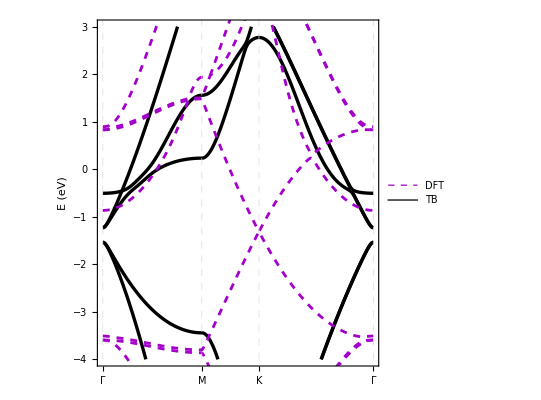

```mathematica
rutaΓMKΓ[n_]:=Module[{ruta1,ruta2,ruta3,ruta4,ruta5,ruta6},
(*This functions creates a path in k space where bands will be calculated*)
ruta1=Table[km(i/n),{i,0,n,2/√3}]; k1=Length[ruta1];
ruta2=Table[km + (kk-km)(i/n),{i,1,n,2}];  k2=k1+Length[ruta2];
ruta3=Table[kk((n-i)/n),{i,1,n}]; k3=k2+Length[ruta3];
Join [ruta1,ruta2,ruta3]];  
rutaKΓMK[n_]:=Module[{ruta1,ruta2,ruta3,ruta4,ruta5,ruta6},
ruta1=Table[kk((n-i)/n),{i,1,n}];k1=Length[ruta1];
ruta2=Table[km(i/n),{i,0,n,2/√3}];  k2=k1+Length[ruta2];
ruta3=Table[km + (kk-km)(i/n),{i,1,n,2}]; k3=k2+Length[ruta3];
Join [ruta1,ruta2,ruta3]
]; 
rutaKMKp[n_]:=Module[{ruta1,ruta2},
ruta1=Table[kk +(km-kk)(i/n),{i,0,n,2/√3}];  k1=Length[ruta1];
ruta2=Table[km + (kp-km)(i/n),{i,1,n,2}]; k2=k1+Length[ruta2];
Join [ruta1,ruta2]
]; 
DFTseq=Sequence[Hue[0.8,1,.8],Dashed,Thickness[0.005]];
TBseq=Sequence[Black,Thickness[0.005]];
TextSeq=Sequence[Black,15,FontFamily->"CMU Serif"];
lgnd=Placed[LineLegend[{Directive[DFTseq],Directive[TBseq]},{Style["DFT",TextSeq],Style["TB",TextSeq]},LegendFunction->(Framed[#,Background->White,FrameStyle->Thickness[1.3]]&),Spacings->0.3],{0.78,0.15}];
(*This function plots the bands: *)
μVHS =μVHSs[[2]];
μ0=μVHS-2.0;
μf=μVHS+1.0;
plt[rangea_,rangeb_,fun1_,fun2_,kpoints_]:=Show[
ListPlot[fun1,Joined->True,PlotRange-> {rangea,rangeb},PlotStyle->{{Hue[0.55,1,0],Thickness[0.006]}}, Frame->True, FrameStyle->Directive[Black,Thick],
FrameTicks->{{Automatic,None},{qpathTicksCs,None}},AspectRatio->1,
GridLines->{(*{k1,k2,k3}*)klabelsCs,{}},
GridLinesStyle->Directive[Dashed], ImageSize->400,FrameTicksStyle->Directive[Black,20],
LabelStyle->Directive[Normal,20,Black,FontFamily->"CMU Serif"],PlotRangePadding->0, FrameLabel->{{"E (eV)",None},{None,None}},AxesOrigin->{0,-1000},PlotLegends->lgnd],
ListPlot[fun2,Joined->True, PlotStyle->{{DFTseq}},Frame->True, FrameStyle->Directive[Black,Thick]]
];
(*
DFTCs=Import[FileNameJoin[{NotebookDirectory[],"DFT_Cs.txt"}],"Table"];
DFTCs=Drop[DFTCs,1];
DFTCs//Dimensions;
n=DeleteDuplicates[DFTCs[[All,1]]];
EnkCsDFT=Table[
l=Select[DFTCs,#[[1]]==i&];
{l[[All,2]]ᵀ,l[[All,3]]}ᵀ,
{i,n}];
*)
DFTCs=ToExpression@Import[FileNameJoin[{NotebookDirectory[],"DFT_Cs_less_orbitals.txt"}],"Table"];
l=Select[DFTCs,Dimensions[#]=={3}&];
EnkCsDFT = {l[[All,1]]ᵀ,l[[All,2]]}ᵀ;
byK=GatherBy[EnkCsDFT,First];
(*turn into {k,{E1,E2,...}} with energies sorted*)
kE={#[[1,1]],Sort[#[[All,2]]]}&/@byK;
nb=Min[Length/@kE[[All,2]]];   (*safest:use min if some k are missing*)
bands=Table[{kE[[All,1]],kE[[All,2,n]]}ᵀ,{n,nb}];
(*Calculate bands along path in k space: *)
kpoints=1000;
rutaq = "ΓMKΓ";
If[rutaq=="ΓMKΓ",
rt=rutaΓMKΓ[kpoints];
qpathTicks={{1,"Γ"},{k1,"M"},{k2,"K"},{k3,"Γ"}},
If[rutaq=="KΓMK",
rt=rutaKΓMK[kpoints];
qpathTicks={{1,"K"},{k1,"Γ"},{k2,"M"},{k3,"K"}},
If[rutaq=="KMKp",
rt=rutaKΓMK[kpoints];
qpathTicks={{1,"K"},{k1,"M"},{k2,"K'"}},
Print["Error in defining path!"]
];
];
];
(*
k=EnkCsDFT[[1]][[All,1]];
*)
k=EnkCsDFT[[All,1]];
klabelsCs={k[[1]],k[[91]],k[[181]],k[[271]]};
qpathTicksCs={{klabelsCs[[1]],"Γ"},{klabelsCs[[2]],"M"},{klabelsCs[[3]],"K"},{klabelsCs[[4]],"Γ"}};

Hrt=Hk[rt];
Ek=Map[Eigenvalues,Hrt];
Ek=Map[Sort,Ek];
Epath = ConstantArray[True,Nb];

(*Do[
Epath[[j]]=Table[{i EnkCsDFT[[1,-1]][[1]]/ 2367,Ek[[i,j]]},{i,Ek//Length}];,
{j,1,Nb}];*)
Do[
Epath[[j]]=Table[{i Max[ EnkCsDFT[[All,1]]]/ 2367,Ek[[i,j]]},{i,Ek//Length}];,
{j,1,Nb}];

ϵa=-4; ϵb=3;
plt[ϵa, ϵb,Epath,bands,kpoints]
```

```mathematica
ImΣ = 0.05;
ReΣ = 0.01;
μ =1;
AEnk =Table[
ReΣ =0.05 (0.1/π)/((ω+0.2)^2+(0.1)^2);
 (ImΣ /π)/((ω-Epath[[All,All,2]] +μ-ReΣ)^2+ImΣ^2),{ω,μ,-4,-0.01}];
AEk =Total[AEnk,{2}];
AEk//Dimensions
```

{501,2367}

```mathematica
MatrixPlot[AEk,ImageSize->700,AspectRatio->0.5]
```

-Graphics-

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"TB_Cs_new.csv"}],Epath]
```

/Users/sherreragonzalez/Documents/Projects/codes/cond_mat/doped-graphene-superlattices/TB_Cs_new.csv

### Lattices

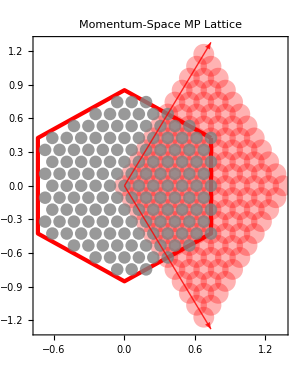

```mathematica
hxg[color_,vv_,kk_,kp_]:={Thickness[vv],color,Line[{kk,kp,kp-kk,-kk,-kp,kk-kp,kk}]}
nkTest=6 2;nchunksTest=1;nqTest= nkTest;
kij=Flatten[IndicesCTchunk[nkTest,nchunksTest,1],1];
kb=kij.{b1,b2};
Graphics[{hxg[Red,0.01,kk,kp],
PointSize[0.05],Red,Opacity[0.3],Point[Flatten[kb,0]],
PointSize[0.03],Gray,Opacity[0.8],Point[Map[CTto1BZ,kij].{b1,b2}],
Thick,Red,Arrow[{{0,0},b1}],Arrow[{{0,0},b2}]},ImageSize->300,Frame->True,PlotLabel->"Momentum-Space MP Lattice"]
```

## Main Functions

### Susceptibility and Screened Interaction

Parameters: {s, ω0, n, δϵ} = {1,17.,1,0.03}

nk= 6

Points in k mesh: 36

μVHS = 4.077

```mathematica
(*Modify only n and nω for more/less resolution. Plots in paper produced with commented values*)
n = 400(*400*); 
nω=150 1(*1500*);
μVHS=μVHSs[[2]];
nk=6n;  
ωf=5;
 ω0=0.;
η=0.01;
FilePath=FileNameJoin[{NotebookDirectory[],"Data_Cs"}];
If[!FileExistsQ[FilePath],
CreateDirectory[FilePath]]
Print["nk= ",nk]
Print["Points in k mesh: ",nk^2]
Print["μVHS = ",μVHS];

Πloop[μkbT_]:=(
 Δω=(ωf-ω0)/nω;
(* ω=Table[ω0+(i-1) Δω,{i,1,nω}]*);
ωc=0.2;
(*dense spacing:10x smaller step*)
Δωdense=Δω/10;
     ω=Join[Range[ω0,ωc-Δωdense,Δωdense],Range[ωc,ωf,Δω]];
nch=nk/3;
solchunks=Table[Table[0,{ω//Length}],{μkbT//Length}];
Print["Diagonalizing and building tensors..."];
Do[
time0=AbsoluteTime[];
kb=Flatten[IndicesCTchunk[nk,nch,ichunk],1].{b1,b2};
Hkb=Hk[kb];
Eψk=Map[Eigensystem,Hkb];
vxk=vx[kb];
Ek=Eψk[[All,1]]; ψk=Eψk[[All,2]];

EkTensor=Flatten[KroneckerProduct[Ek,e]];
EkqTensor=Flatten[KroneckerProduct[e,Ek]];
ΔE=EkTensor-EkqTensor;
EkEkq={EkTensor,EkqTensorᵀ}ᵀ;
Fv=Flatten[Table[Norm[ψk[[i,n]]*ᵀ.vxk[[i]].ψk[[i,m]]]^2,{i,1,vxk//Length},{n,1,Nb},{m,1,Nb}],2];
Do[
μ=μkbT[[l,1]];
kbT=μkbT[[l,2]];
ΔETensor=(EkEkq-μ)/kbT;

Πk=ΔfΔϵ[ΔETensor]*Fv/kbT ;
solchunks[[l]]+=(2 Norm[b1]^2)/(4 π^2 nk^2)Map[Total[Πk/(ΔE+ⅈ η+#)]&,ω];
,{l,1,μkbT//Length}];
If[ichunk==1, Print["Estimated time: ",(AbsoluteTime[]-time0)*nch/60, " mins"]]
,{ichunk,1,nch}];
solchunks)
```

nk= 2400

Points in k mesh: 5760000

μVHS = 0.839523

```mathematica
(*IF file with same parameters exists, it imports it instad of recalculating!!!!!*)
Temp=1;
μ0=μVHS-2.0;
μf=μVHS+1.0;
δμ=0.1;
Print["Parameters: {n, Temp, η, ω0, ωf, nω} = ",{n, Temp, η,ω0,ωf,nω}]
ParamString=ToString[n]<>"_"<>ToString[Temp]<>"_"<>ToString[η]<>"_"<>ToString[ω0]<>"_"<>ToString[ωf]<>"_"<>ToString[nω];
DataPath=FileNameJoin[{FilePath,ParamString}];
If[!FileExistsQ[DataPath],
CreateDirectory[DataPath]];
FillingPath=FileNameJoin[{DataPath,"filling_"<>ToString[μ0]<>"_"<>ToString[μf]<>"_"<>ToString[δμ]}];
SigmaPath=FileNameJoin[{FillingPath,"σ.csv"}];
μlistkbT=Table[{i,kBoltz Temp },{i,μ0,μf,δμ}];
If[FileExistsQ[SigmaPath],
σ=ToExpression@Import[SigmaPath];
Print["Importing data. Done"];,
Print["No data found. Calculating..."];
Πω=Πloop[μlistkbT];
σ=Map[{ωᵀ,#}ᵀ&,Im[Πω]];
Export[SigmaPath,σ];
Print["Completed."];
];
```

Parameters: {n, Temp, η, ω0, ωf, nω} = {400,1,0.01,0.,5,150}

Importing data. Done

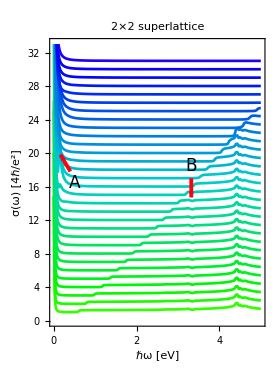
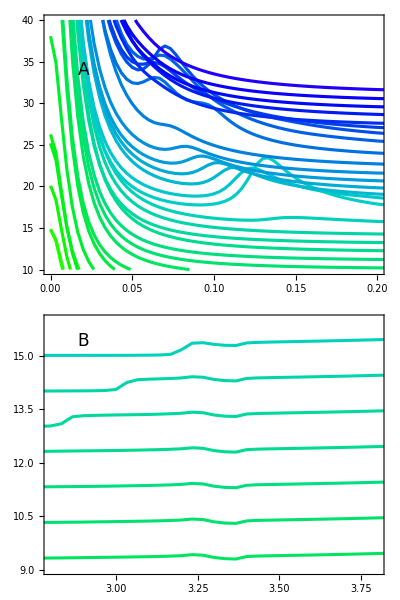

```mathematica
ColsMag[x_]:=Blend[{{0.,Hue[0.99]},{1,Hue[0.65]}},x];
ColsPy[x_]:=Blend[{{0,Hue[0.3]},{0.5,Hue[0.5,1,0.8]},{1,Hue[0.7]}},x];
ColsG[x_]:=Blend[{{0.,Hue[0.2,1,1]},{0.5,Hue[0.1]},{1,Hue[0.0]}},x];
Cols=ColsPy;
nμc=(μlistkbT//Length);
μColors= Table[{Cols[i/nμc],Thickness[0.007]},{i,0,nμc}];
μColorsi= Table[{Cols[i/nμc],Thickness[0.015]},{i,0,nμc}];
PlotSeq=Sequence[Joined->True,Frame->True,FrameStyle->Directive[Black,Thick],FrameTicksStyle->Directive[Black,15,FontFamily->"CMU Serif"],
LabelStyle->Directive[Normal,15,FontFamily->"CMU Serif"],AspectRatio-> 2 0.7,ImageSize->250];
ColLeg=BarLegend[{Cols,{0,1}},LegendLabel->"μ", LabelStyle->Directive[15,Black,FontFamily->"CMU Serif"],"Ticks"->{(*0,1*)},"TickLabels"->{(*"Away from vHS",*)" "},ImageSize->100];
ArrowSeq=Sequence[Hue[0.99],Arrowheads[0.05],Thickness[0.01]];
RecSeq=Sequence[EdgeForm[Gray],Opacity[0]];
TextSeq=Sequence[Black,17,FontFamily->"CMU Serif",Background->White];
LineSeq=Sequence[Gray,Dashed];
δσ=1;
PltR={{ω0,ωf},{0,33}};
PltRi1={{0,.2},{10,40}};
PltRi2={{3,4}-0.2,{11,18}-2};
σCurves=Table[{σ[[i,All,1]]ᵀ,σ[[i,All,2]]+i δσ}ᵀ,{i,σ//Length}];
plot=ListPlot[σCurves,PlotStyle->μColors,PlotSeq,
PlotRange->PltR,
FrameLabel->{"ℏω [eV]","σ(ω) [4ℏ/e^2]"},PlotLabel->Style[(*"Cs-doped SLG"*)"2×2 superlattice",Black],Epilog->{
ArrowSeq,Arrow[{{3.52-0.2,18-1},{3.52-0.2,15.7-1}}],Arrow[{{0.4,17.8},{0.16,19.8}}],
(*RecSeq,Rectangle[PltRi1ᵀ[[1]],PltRi1ᵀ[[2]]],Rectangle[PltRi2ᵀ[[1]],PltRi2ᵀ[[2]]]*)
Text[Style["A",TextSeq],{0.5,16.4}],
Text[Style["B",TextSeq],{3.52-0.2,18.5}]
}];
inset1=ListPlot[σCurves,PlotStyle->μColorsi,ImageSize->150,AspectRatio->1,PlotSeq,PlotRange->PltRi1,Epilog->{Text[Style["A",TextSeq],{0.02,34}]}];
inset2=ListPlot[σCurves,PlotStyle->μColorsi,ImageSize->146,AspectRatio->1,PlotSeq,PlotRange->PltRi2,Epilog->{Text[Style["B",TextSeq],{2.9,15.4}]}];
plt=Row[{plot,Column[{inset1,inset2}](*,ColLeg*)}]
Export[FileNameJoin[{NotebookDirectory[],"Sigma_CsG.pdf"}],plt];
```